# MA2330

## 5.7 Summary

The solution of y'=A y associated with a real eigen value λ is 
	y(t)=ⅇ^(λ t)v 
where v is a matching eigenvector.

The solutions of y'=A y associated with a complex conjugate eigenvalue λ=a±b ⅈ are
	y_1(t) | = | ⅇ^(a t)(cos(b t) re(v)-sin(b t) im(v))
y_2(t) | = | ⅇ^(a t)(sin(b t) re(v)+cos(b t) im(v))
where v = re(v)±im(v) ⅈ are matching eigenvectors.

Eigenvalues of A give the long time behavior of the Dynamical System x'=A x

Complex a± b ⅈ are spirals in the re(v)—im(v) plane.

Spiral in for a<0 and out for a>0.

Spin fast for big b

Real λ<0 are attracting.

Real λ>0 are repelling.

```mathematica
Clear[ODEArrows]
ODEArrows[{λ_Real,v_}]:=If[λ>0, 
{Cyan,Thick,Arrow[{0*v, v}], Arrow[{0*v,-v}]},
{Green,Thick,Arrow[{v,0*v}], Arrow[{-v,0*v}]}
]
ODEArrows[{λ_Complex,v_}]:=Module[
{a,b, tMax},
{a,b}=ReIm[λ];
{If[a<0,Blue,Red],Table[
Arrow[
Table[E^(a t)(Cos[b t+θ] Re[v]- Sin[b t+θ] Im[v]),
{t, -Log[2]/Abs[a],Log[2]/Abs[a], 0.1*Log[2]/Abs[a]}
]],{θ,0, π,π/6}]}
]
```

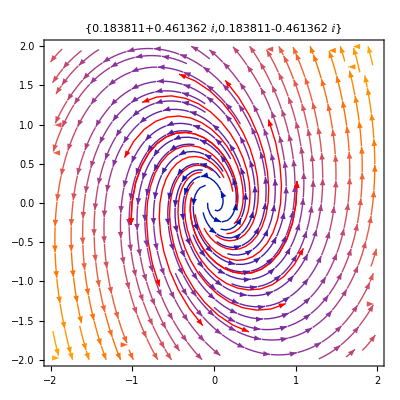

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];
{λ,V}=Chop[Eigensystem[A]];
StreamPlot[ A.{x1,x2},{x1,-2,2},{x2,-2,2},
PlotLabel->λ,
Epilog->Map[ODEArrows,{λ,V}ᵀ]]
```

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];
{λ,V}=Chop[Eigensystem[A]];
Show[
StreamPlot3D[A.{x1,x2,x3},{x1,-2,2},{x2,-2,2},{x3,-2,2},
StreamMarkers->"Arrow",
StreamStyle->Opacity[0.5]],
Graphics3D[Map[ODEArrows,{λ,V}ᵀ]],
PlotLabel->λ]
```

-Graphics3D-

## 5.8 Power Method x_(k+1)=A x_k

Computers order eigenvalues |λ_1|≥|λ_2|≥…≥|λ_n|. And normalize the eigenvectors ||v_i||=1.

If |λ_1| >|λ_2|then there is a simple way to compute the eigen vector associated with λ_1.  All you have to do is pick a random vector 
	x_0=c_1 v_1+c_(2 v_2)…+c_n v_n=∑_(j=1)^n c_i v_i
then the iterates x_k=A x_(k-1) converge to a multiple of v_1
	x_k=c_1 λ_1^k v_1+c_2 λ_2^k v_2+…+c_n λ_n^k v_n=∑_(j=1)^n c_i λ_i^k v_i
scale everything by λ_1^k to get
	x_k λ_1^-k=c_1 v_1+(c_2(λ_2/λ_1))^k v_2+…+(c_2(λ_n/λ_1))^k v_n→ c_1 v_1
In practice, any scaling works.  You do not need to know the eigenvalue.  This is called the power method.

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
x=RandomReal[{-1,1},m];
maxIter=33;
Data=Table[x=Normalize[A.x],{maxIter}];
TableForm[Data,TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | -0.428636 | -0.526224 | -0.249212 | -0.276077 | 0.288756 | 0.563608
2 | 0.828079 | 0.353859 | 0.206643 | -0.0214829 | -0.347925 | -0.157652
3 | -0.717063 | -0.348023 | -0.225186 | 0.149405 | 0.434061 | 0.321343
4 | 0.733619 | 0.401495 | 0.23303 | -0.0155951 | -0.301134 | -0.394178
5 | -0.746127 | -0.409913 | -0.256626 | 0.0171262 | 0.352376 | 0.291456
6 | 0.746223 | 0.369134 | 0.227531 | -0.0712313 | -0.383812 | -0.320524
7 | -0.738964 | -0.394194 | -0.238005 | 0.043588 | 0.346754 | 0.34606
8 | 0.744717 | 0.395643 | 0.243011 | -0.0358579 | -0.353023 | -0.322332
9 | -0.744371 | -0.386018 | -0.237059 | 0.050735 | 0.365037 | 0.323849
10 | 0.742603 | 0.389866 | 0.237747 | -0.0464905 | -0.356532 | -0.332784
11 | -0.743544 | -0.392021 | -0.23994 | 0.0425867 | 0.35595 | 0.327683
12 | 0.743853 | 0.389329 | 0.238522 | -0.046261 | -0.359684 | -0.326651
13 | -0.743305 | -0.389837 | -0.238368 | 0.0459964 | 0.358054 | 0.329222
14 | 0.743465 | 0.390659 | 0.23901 | -0.0446476 | -0.357364 | -0.328357
15 | -0.743604 | -0.390048 | -0.238755 | 0.0454281 | 0.358367 | 0.327751
16 | 0.743472 | 0.39002 | 0.238622 | -0.0455825 | -0.358144 | -0.328404
17 | -0.743481 | -0.390281 | -0.238792 | 0.0451903 | 0.357851 | 0.328322
18 | 0.74353 | 0.390162 | 0.23876 | -0.0453241 | -0.358088 | -0.3281
19 | -0.743502 | -0.390116 | -0.238708 | 0.0454155 | 0.358088 | 0.328244
20 | 0.743496 | 0.390187 | 0.238747 | -0.0453158 | -0.357992 | -0.328261
21 | -0.74351 | -0.39017 | -0.238748 | 0.0453287 | 0.35804 | 0.328194
22 | 0.743506 | 0.39015 | 0.238732 | -0.0453625 | -0.358055 | -0.328221
23 | -0.743502 | -0.390167 | -0.238739 | 0.0453404 | 0.358028 | 0.328235
24 | 0.743506 | 0.390167 | 0.238742 | -0.0453378 | -0.358035 | -0.328217
25 | -0.743505 | -0.39016 | -0.238738 | 0.045348 | 0.358042 | 0.32822
26 | 0.743504 | 0.390163 | 0.238739 | -0.0453439 | -0.358036 | -0.328226
27 | -0.743505 | -0.390164 | -0.23874 | 0.0453419 | 0.358036 | 0.328222
28 | 0.743505 | 0.390162 | 0.238739 | -0.0453445 | -0.358039 | -0.328221
29 | -0.743505 | -0.390163 | -0.238739 | 0.045344 | 0.358037 | 0.328223
30 | 0.743505 | 0.390164 | 0.23874 | -0.0453432 | -0.358037 | -0.328222
31 | -0.743505 | -0.390163 | -0.238739 | 0.0453438 | 0.358038 | 0.328222
32 | 0.743505 | 0.390163 | 0.238739 | -0.0453439 | -0.358037 | -0.328223
33 | -0.743505 | -0.390163 | -0.238739 | 0.0453436 | 0.358037 | 0.328222

```mathematica
Eigensystem[A,1]
```

{{-2.14747},{{-0.743505+0. ⅈ,-0.390163+0. ⅈ,-0.238739+0. ⅈ,0.0453437+0. ⅈ,0.358037+0. ⅈ,0.328222+0. ⅈ}}}

### Inverse Power Method x_(k+1)=(A-α I)^-1 x_k

The inverse power method 
	x_(k+1)=(A-α I)^-1 x_k
converges to an eigenvector with an eigenvalue near α.

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
x=RandomReal[{-1,1},m];
α=1.2;
maxIter=50;
Data=Table[x=Normalize[LinearSolve[A-α IdentityMatrix[m],x]],{maxIter}];
TableForm[Data,TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | 0.505508 | 0.0709446 | -0.612896 | 0.208731 | 0.515217 | -0.234029
2 | 0.561128 | 0.163649 | -0.503016 | 0.146337 | 0.5107 | -0.350857
3 | 0.556756 | 0.159422 | -0.507608 | 0.147777 | 0.510143 | -0.353353
4 | 0.5568 | 0.159405 | -0.507624 | 0.147754 | 0.510229 | -0.353152
5 | 0.556803 | 0.159411 | -0.50762 | 0.147754 | 0.510226 | -0.353154
6 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
7 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
8 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
9 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
10 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
11 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
12 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
13 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
14 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
15 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
16 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
17 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
18 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
19 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
20 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
21 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
22 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
23 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
24 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
25 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
26 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
27 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
28 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
29 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
30 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
31 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
32 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
33 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
34 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
35 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
36 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
37 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
38 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
39 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
40 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
41 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
42 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
43 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
44 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
45 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
46 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
47 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
48 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
49 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154
50 | 0.556803 | 0.15941 | -0.50762 | 0.147754 | 0.510226 | -0.353154

### Summary Power Method

The power method 
	y_(k+1) | = | A x_k
x_(k+1) | = | (y_(k+1))/(||y_(k+1)||)
converges to the eigenvector with the  "largest" eigenvalue.

The inverse power method 
	y_(k+1) | = | (A-α Id)^-1 x_k
x_(k+1) | = | (y_(k+1))/(||y_(k+1)||)
 converges to the eigenvector with the  eigenvalue "nearest" the shift α.

## 5.9 Markov Chains

A vector x with nonnegative entries that sum to one is a probability vector.

A square matrix P with non-negative entries and columns that sum to one is a  stochastic matrix

The Discrete Dynamical System x_k=P x_(k-1) with a stochastic matrix P and a probability vector x_0 as initial state is a Markov Chain.

The car matrix from exam 1 
	P=(0.9 | 0.1 | 0.3 | 0.2
0.1 | 0.8 | 0 | 0
0 | 0.1 | 0.7 | 0
0 | 0 | 0 | 0.8)	
is a stochastic matrix.  If we normalize the initial car vector by 428 (the total number of cars) we get
	x_0=(100
85
120
123)/428=(0.233645
0.198598
0.280374
0.287383)
This is a Markov chain.  It is not an accident that P has an eigen value of 1.

Theorem 10 : If P is a stochastic matrix then 1 is an eigenvalue of P.

Why?  P and Pᵀ have the same eigenvalues and since Pᵀ has row sums equal to one the vector of all ones is an eigenvector.

```mathematica
P=({{0.9, 0.1, 0.3, 0.2}, {0.1, 0.8, 0, 0}, {0, 0.1, 0.7, 0}, {0, 0, 0, 0.8}});
Pᵀ.{1,1,1,1}
```

{1.,1.,1.,1.}

A steady state vector satisfies P v =v.

A steady state vector is an eigenvector associated with the eigenvalue 1.

Theorem 11
Regular Markov chains x_k=P x_(k-1) converge to a unique steady state vector as k→∞.

A Markov Chain is  Regular if some matrix power P^k has strictly positive entries.

Regular means is that all the states are linked.